```mathematica
Clear["Global`*"]
(*name="student@10.0.1.9://home/student/BEM/Kramer2021_0d03/result.json"*)
(*data01DLPF4=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/LPF4/01D_LPF4.txt"}],"Data"];
data01DFNPF1=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/FNPF1/01D_FNPF1.txt"}],"Data"];
data01DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/01D_CI95_Normalized.txt"}],"Data"];
data03DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/03D_Measured1_Normalized.txt"}],"Data"];
data05DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/05D_Measured1_Normalized.txt"}],"Data"];
*)
name="~/BEM/Ren2015/result.json"
Quiet[Z=(data="float_COM"/.Import[name])[[;;,3]];];
Quiet[X=(data="float_COM"/.Import[name])[[;;,1]];];
Quiet[Pitch=(data="float_pitch"/.Import[name]);];
Quiet[Vx=(data="float_velocity"/.Import[name])[[;;,1]];];
Quiet[Vy=(data="float_velocity"/.Import[name])[[;;,2]];];
Quiet[Vz=(data="float_velocity"/.Import[name])[[;;,3]];];
Quiet[time="time"/.Import[name];];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
H0=30/1000;
```

```mathematica
Import[name][[;;,1]]
```

{float_accel,float_velocity,float_COM,float_force,float_torque,float_EK,float_EP,float_area,float_pitch,float_roll,float_yaw,time,water_E,water_EK,water_EP,water_volume}

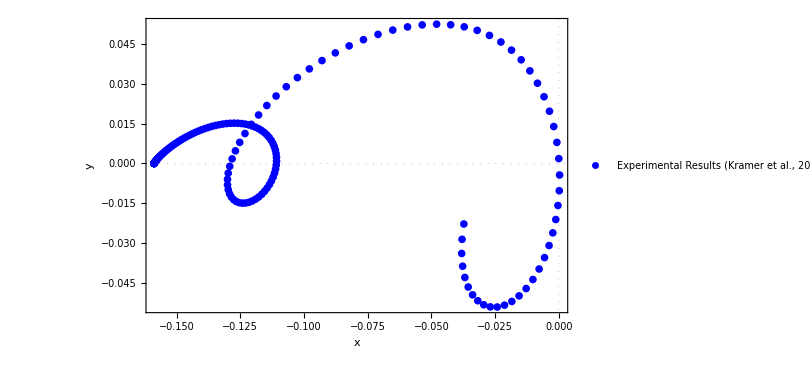

```mathematica
ListPlot[
{X-2.3088,Z-0.4}ᵀ,
Joined->{False,True},
PlotStyle->{{Blue,Dashed},Red},
BaseStyle->{FontFamily->"Times"},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{Automatic,Automatic},
(*AspectRatio->1/2,*)
(*GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},*)
Frame->True,
FrameLabel->{
Style["x",FontSize->20,FontFamily->"Times",Italic],
Style["y",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]
]
```

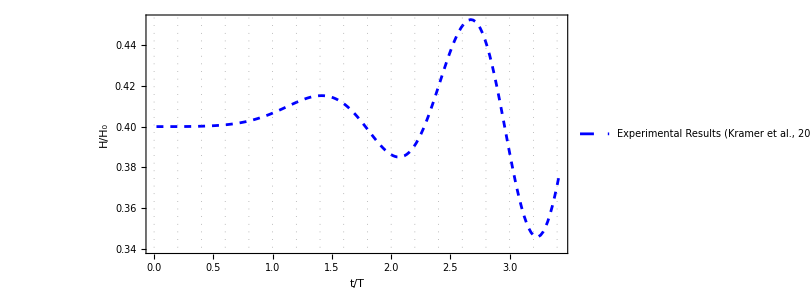

```mathematica
fig=ListPlot[
{time,Z}ᵀ,
Joined->{True,True},
PlotStyle->{{Blue,Dashed},Red},
BaseStyle->{FontFamily->"Times"},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{Automatic,Automatic},
AspectRatio->1/2,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H/H_0",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]
]
```

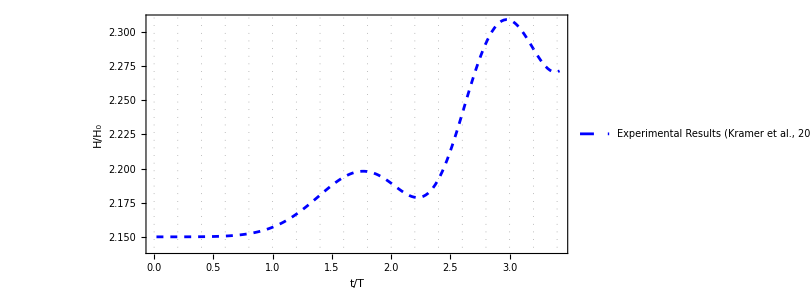

```mathematica
ListPlot[
{time,X}ᵀ,
Joined->{True,True},
PlotStyle->{{Blue,Dashed},Red},
BaseStyle->{FontFamily->"Times"},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{Automatic,Automatic},
AspectRatio->1/2,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H/H_0",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]
]
```

```mathematica
ListPlot[
{time,Pitch}ᵀ,
Joined->{True,True},
PlotStyle->{{Blue,Dashed},Red},
BaseStyle->{FontFamily->"Times"},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{Automatic,Automatic},
AspectRatio->1/2,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H/H_0",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]
]
```

Transpose::nmtx: {{0.02,0.0366682,0.0529897,0.07178,0.09178,0.11178,0.13178,0.15178,0.17178,0.19178,«162»},String[]}の最初の2個のレベルは転置できません．

ListPlot::lpn: Transpose[{{0.02,0.0366682,0.0529897,0.07178,0.09178,0.11178,0.13178,0.15178,0.17178,0.19178,«162»},String[]}]は数値のリストあるいは数値の対のリストではありません．

ListPlot[Transpose[{{0.02,0.0366682,0.0529897,0.07178,0.09178,0.11178,0.13178,0.15178,0.17178,0.19178,0.21178,0.23157,0.25157,0.27157,0.29157,0.31157,0.33157,0.35157,0.37157,0.39157,0.41157,0.43157,0.45157,0.47157,0.49157,0.51157,0.53157,0.55157,0.57157,0.59157,0.61157,0.63157,0.65157,0.67157,0.69157,0.71157,0.73157,0.75157,0.77157,0.79157,0.81157,0.83157,0.85157,0.87157,0.89157,0.91157,0.93157,0.95157,0.97157,0.99157,1.01157,1.03157,1.05157,1.07157,1.09157,1.11157,1.13157,1.15157,1.17157,1.19157,1.21157,1.23157,1.25157,1.27157,1.29157,1.31157,1.33157,1.35157,1.37157,1.39157,1.41157,1.43157,1.45157,1.47157,1.49157,1.51157,1.53157,1.55157,1.57157,1.59157,1.61157,1.63157,1.65157,1.67157,1.69157,1.71157,1.73157,1.75157,1.77157,1.79157,1.81157,1.83157,1.85157,1.87157,1.89157,1.91157,1.93157,1.95157,1.97157,1.99157,2.01157,2.03157,2.05157,2.07157,2.09157,2.11157,2.13157,2.15157,2.17157,2.19157,2.21157,2.23157,2.25157,2.27157,2.29157,2.31157,2.33157,2.35157,2.37157,2.39157,2.41157,2.43157,2.45157,2.47157,2.49157,2.51157,2.53157,2.55157,2.57157,2.59157,2.61157,2.63157,2.65157,2.67157,2.69157,2.71157,2.73157,2.75157,2.77157,2.79157,2.81157,2.83157,2.85157,2.87157,2.89157,2.91157,2.93157,2.95157,2.97157,2.99092,3.00941,3.02751,3.04547,3.06352,3.08197,3.10114,3.12114,3.14114,3.16114,3.18114,3.20114,3.22114,3.24114,3.26114,3.28114,3.30114,3.32114,3.34114,3.36114,3.38114,3.40114,3.42114},String[]}],Joined→{True,True},PlotStyle→{{RGBColor[0, 0, 1],Dashing[{Small,Small}]},RGBColor[1, 0, 0]},BaseStyle→{FontFamily→Times},PlotRange→{Automatic,Automatic},AspectRatio→1/2,GridLines→{{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.},{-1.,-0.5,0.,0.5,1.}},Frame→True,FrameLabel→{t/T,H/H_0},FrameStyle→Directive[FontSize→20,GrayLevel[0],Thickness[0.002]],GridLines→{{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.},{-1.,-0.5,0.,0.5,1.}},GridLinesStyle→Directive[GrayLevel[0.5],Dashing[{0,Small}]],ImageSize→600,PlotLegends→Placed[LineLegend[{Experimental Results (Kramer et al., 2021),Numerical Simulation (BEM)},LegendMarkerSize→20,LabelStyle→15],{0.65,0.15}]]